```mathematica
b=NDSolve[{y''[t]+(y'[t]+1)^2*y'[t]+y[t]==0,y[0]==1,y'[0]==0},y[t],{t,0,10}]
```

{{y[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

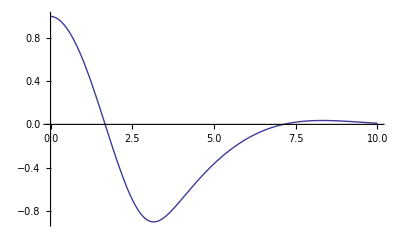

```mathematica
Plot[Evaluate[y[t]/.b],{t,0,10}]
```

```mathematica
DSolve[{L*Q''[t]+R*Q'[t]+1/C*Q[t]==Subscript[V, 0]*ⅇ^(j*ω*t)},Q[t],t]
```

{{Q[t]→ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)) C[1]+ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)) C[2]-(2 C L (√C ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) R-√C ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) R+ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) √(-4 L+C R^2)+ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) √(-4 L+C R^2)+2 √C ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) j L ω-2 √C ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) j L ω) V_0)/(√(-4 L+C R^2) (-√C R+√(-4 L+C R^2)-2 √C j L ω) (√C R+√(-4 L+C R^2)+2 √C j L ω))}}